```mathematica
loadTmeSeriesResampled=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"]
```

TimeSeries[…]

```mathematica
loadTSModelDefault=TimeSeriesModelFit[timeSeriesResampled]
```

TimeSeriesModel[…]

```mathematica
loadTSModelDefault["ParameterTable"]
```

General::munfl: 6.628959565280767552514×10^-12373 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.269616311694080793446×10^-3517 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 1.64257 | 0.00529501 | 310.211 | 0.
𝒶_2 | -0.697632 | 0.00511084 | -136.501 | 0.
𝒷_1 | -0.131058 | 0.00634279 | -20.6625 | 8.18371×10^-95
𝒷_2 | 0.159042 | 0.00513928 | 30.9464 | 6.83169×10^-209

```mathematica
loadTSModelSARIMA=TimeSeriesModelFit[timeSeriesResampled,{"SARIMA",{Automatic,Automatic,Automatic}}]
```

TimeSeriesModel[…]

```mathematica
loadTSModelSARIMA["CandidateSelectionTable"]
```

| Candidate | AIC
1 | ARMAProcess[2,2] | 726281.
2 | ARMAProcess[2,1] | 726380.
3 | SARMAProcess[{2,2},{0,1}_30] | 726764.
4 | ARMAProcess[2,3] | 728155.
5 | ARMAProcess[3,2] | 730347.
6 | ARMAProcess[3,3] | 730413.
7 | SARMAProcess[{2,2},{1,0}_30] | 736828.
8 | SARMAProcess[{2,2},{1,1}_30] | 737547.
9 | ARMAProcess[1,2] | 737553.
10 | SARMAProcess[{1,1},{1,0}_30] | 746304.

```mathematica
loadTSModelSARIMA["ParameterTable"]
```

General::munfl: 6.628959565280767552514×10^-12373 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.269616311694080793446×10^-3517 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 1.64257 | 0.00529501 | 310.211 | 0.
𝒶_2 | -0.697632 | 0.00511084 | -136.501 | 0.
𝒷_1 | -0.131058 | 0.00634279 | -20.6625 | 8.18371×10^-95
𝒷_2 | 0.159042 | 0.00513928 | 30.9464 | 6.83169×10^-209

```mathematica
loadTSModelSARMA=TimeSeriesModelFit[timeSeriesResampled,{"SARMA"}]
```

TimeSeriesModel[…]

```mathematica
loadTSModelSARMA["CandidateSelectionTable"]
```

| Candidate | AIC
1 | ARMAProcess[2,2] | 726281.
2 | ARMAProcess[2,1] | 726380.
3 | SARMAProcess[{2,2},{0,1}_12] | 726494.
4 | ARMAProcess[2,3] | 728155.
5 | ARMAProcess[3,2] | 730347.
6 | ARMAProcess[3,3] | 730413.
7 | SARMAProcess[{2,2},{1,0}_12] | 732798.
8 | SARMAProcess[{2,2},{1,1}_12] | 732922.
9 | ARMAProcess[1,2] | 737553.
10 | SARMAProcess[{1,1},{1,1}_12] | 747230.

```mathematica
loadTSModelSARMA["ParameterTable"]
```

General::munfl: 6.628959565280767552514×10^-12373 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.269616311694080793446×10^-3517 is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 1.64257 | 0.00529501 | 310.211 | 0.
𝒶_2 | -0.697632 | 0.00511084 | -136.501 | 0.
𝒷_1 | -0.131058 | 0.00634279 | -20.6625 | 8.18371×10^-95
𝒷_2 | 0.159042 | 0.00513928 | 30.9464 | 6.83169×10^-209

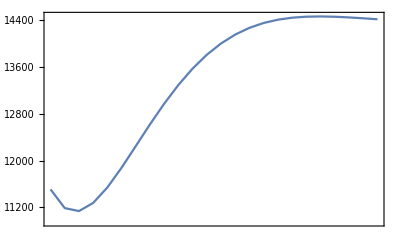

```mathematica
DateListPlot[TimeSeriesForecast[loadTSModelSARMA,{24}]]
```

```mathematica
loadTSModelGARCH=TimeSeriesModelFit[timeSeriesResampled,{"GARCH"}]
```

FindMinimum::sdir: Search direction has become too small.

TimeSeriesModel[…]

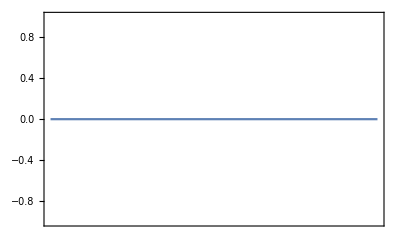

```mathematica
DateListPlot[TimeSeriesForecast[loadTSModelGARCH,{24}]]
```